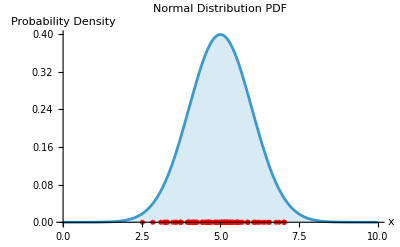

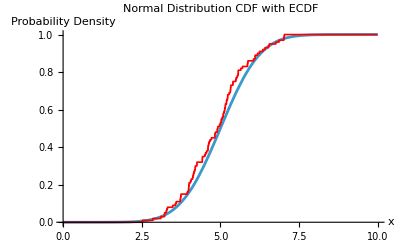

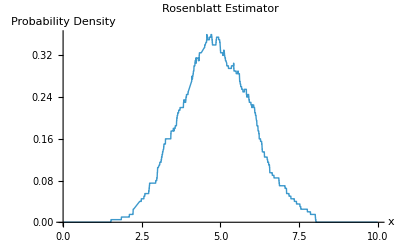

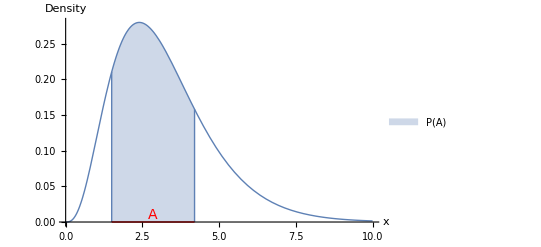

```mathematica
(*Section 2 Plots and Rosenblatt Estimator*)
(*Normal(5,1) density and plot*)
SeedRandom[123];
Norm51=NormalDistribution[5,1];
DataN51=RandomVariate[Norm51,100];

PlotN51 =Show[Plot[PDF[Norm51,x],{x,0,10},PlotLabel->"Normal Distribution PDF",
AxesLabel->{"x","Probability Density"},
PlotLegends->{""},
Filling->Axis],ListPlot[Transpose@{DataN51,ConstantArray[0,Length[DataN51]]},PlotStyle->{Red,Opacity[0.9]}]]


(*CDF vs Empirical CDF plot, where we use ListStepPlot to make the ECDF with the data points defined below*)
FnData=Transpose@{Sort[DataN51],Range[Length[DataN51]]/Length[DataN51]};
FnDataExtended=Join[{{0,0}},FnData,{{10,FnData[[-1,2]]},{10,1}}]; (*this extension was necessary to include the (0,0) and (1,1) points for ListStepPlot*)

PlotN51CDF = Show[Plot[CDF[Norm51,x],{x,0,10},PlotLabel->"Normal Distribution CDF with ECDF",
AxesLabel->{"x","Probability Density"},
PlotLegends->{""}],ListStepPlot[FnDataExtended,PlotStyle->{Red,Thickness[0.003]},PlotRange->{0,1}, PlotLegends->{""}]]

(*Rosenblatt Estimator Construction and plot, which is equivalent to the KDE on R with the rectangular kernel*)
RectKer[u_?NumericQ]:=Piecewise[{{1/2,Abs[u]<=1}},0]

KDERosen[x_?NumericQ,h_,data_] := 1/(h*Length[data])Sum[RectKer[(xi-x)/h],{xi,data}];

RosenblattPlot=Plot[KDERosen[x,1, DataN51],{x,0,10},PlotLabel->"Rosenblatt Estimator",AxesLabel->{"x","Probability Density"},Filling->None,PlotStyle->Thin]

(*Probability Region Gamma Density Plot*)
dist=GammaDistribution[4,0.8];

(*Region A of interest*)
a=1.5;
b=4.2;

(*Blue colour seen in the other plots of this section*)
blue=ColorData[97][1]; 

(*Used to plot the probability region in the below plot*)
regionPts=Join[{{a,0}},Table[{x,PDF[dist,x]},{x,a,b,0.01}],{{b,0}}];

PlotGamma = Legended[Plot[PDF[dist,x],{x,0,10},PlotStyle->{blue,Thick},Axes->True,AxesLabel->{"x","Density"},PlotRange->All,Epilog->{{Directive[Opacity[0.3],blue],EdgeForm[None],Polygon[regionPts]},{blue,Thin,Line[{{a,0},{a,PDF[dist,a]}}],Line[{{b,0},{b,PDF[dist,b]}}]},{Directive[Red,Opacity[1],Thick],Line[{{a,0},{b,0}}]},{Directive[Red,Opacity[1]],Text[Style["A",14],{(a+b)/2,0.01}]}}],SwatchLegend[{Directive[Opacity[0.3],blue]},{"P(A)"}]]
```